```mathematica
With[{max=58716},Monitor[Table[ContainsRule1Reduction[k],{k,1,max}],{k,N[k/max * 100]}]]
```

```mathematica
3*24
```

72

```mathematica
Map[{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],VertexCount[ReadGrof[#[[3]]]]}&,
Select[
Map[{Chrom[#[[1]]],Chrom[#[[2]]],#[[1]],#[[2]],#[[3]]}&,Take[deps2,10000]]
,#[[1]]==5*24&&#[[2]]==3*24&]
]
```

{{120,72,7,18,{2,1<->5,2<->7},7},{120,72,11,40,{2,3<->6,2<->4},8},{120,72,11,36,{2,3<->4,6<->8},8},{120,72,49,142,{2,3<->6,2<->4},9},{120,72,49,143,{2,3<->4,6<->8},9},{120,72,26,88,{2,2<->6,3<->9},9},{120,72,26,160,{2,5<->8,3<->4},9},{120,72,26,119,{2,4<->5,8<->9},9},{120,72,39,97,{2,1<->7,2<->5},9},{120,72,39,113,{2,2<->7,1<->9},9},{120,72,39,180,{2,5<->7,1<->6},9},{120,72,47,99,{2,3<->6,2<->4},9},{120,72,47,165,{2,3<->4,6<->8},9},{120,72,47,160,{2,2<->5,6<->7},9},{120,72,47,88,{2,3<->8,4<->7},9},{120,72,31,114,{2,3<->6,2<->8},9},{120,72,31,197,{2,5<->7,2<->9},9},{120,72,31,155,{2,3<->9,7<->8},9},{120,72,42,180,{2,2<->6,3<->9},9},{120,72,42,255,{2,1<->9,2<->7},9},{120,72,45,217,{2,2<->7,1<->6},9},{120,72,45,153,{2,2<->6,7<->9},9},{120,72,45,142,{2,2<->9,3<->6},9},{120,72,145,397,{2,3<->6,2<->4},10},{120,72,145,398,{2,3<->4,6<->8},10},{120,72,145,401,{2,5<->7,2<->8},10},{120,72,145,402,{2,3<->8,4<->7},10},{120,72,161,429,{2,2<->6,3<->9},10},{120,72,161,430,{2,3<->6,2<->8},10},{120,72,161,437,{2,4<->5,8<->9},10},{120,72,161,438,{2,5<->9,2<->4},10},{120,72,162,464,{2,2<->6,3<->9},10},{120,72,162,465,{2,3<->6,2<->8},10},{120,72,162,468,{2,4<->5,8<->9},10},{120,72,162,472,{2,6<->8,3<->4},10},{120,72,162,473,{2,5<->9,2<->4},10},{120,72,96,635,{2,1<->7,2<->5},10},{120,72,96,636,{2,2<->7,1<->10},10},{120,72,96,637,{2,5<->7,1<->6},10},{120,72,96,644,{2,3<->10,2<->6},10},{120,72,76,560,{2,5<->8,3<->4},10},{120,72,76,346,{2,4<->5,8<->10},10},{120,72,76,537,{2,3<->6,8<->9},10},{120,72,76,629,{2,6<->9,3<->10},10},{120,72,76,536,{2,5<->10,4<->9},10},{120,72,235,685,{2,3<->6,2<->4},10},{120,72,235,665,{2,3<->4,6<->8},10},{120,72,235,666,{2,2<->5,6<->7},10},{120,72,235,351,{2,3<->8,4<->7},10},{120,72,98,637,{2,2<->6,3<->10},10},{120,72,98,908,{2,1<->10,2<->7},10},{120,72,211,465,{2,2<->6,3<->10},10},{120,72,211,725,{2,1<->7,5<->10},10},{120,72,211,491,{2,1<->10,2<->7},10},{120,72,179,464,{2,1<->7,2<->5},10},{120,72,179,817,{2,2<->7,1<->9},10},{120,72,179,725,{2,5<->7,1<->6},10},{120,72,179,472,{2,6<->7,5<->9},10},{120,72,179,722,{2,3<->9,2<->6},10},{120,72,219,438,{2,3<->4,5<->8},10},{120,72,219,430,{2,2<->8,3<->6},10},{120,72,219,461,{2,2<->6,8<->10},10},{120,72,132,536,{2,3<->8,5<->10},10},{120,72,132,729,{2,5<->8,3<->9},10},{120,72,132,715,{2,4<->6,9<->10},10},{120,72,132,537,{2,6<->9,4<->5},10},{120,72,132,556,{2,6<->10,3<->4},10},{120,72,89,550,{2,3<->9,2<->6},10},{120,72,89,528,{2,5<->10,6<->7},10},{120,72,89,608,{2,6<->10,5<->9},10},{120,72,89,551,{2,2<->10,7<->9},10},{120,72,89,840,{2,7<->10,2<->5},10},{120,72,90,524,{2,3<->6,8<->9},10},{120,72,90,1169,{2,3<->8,6<->10},10},{120,72,90,723,{2,3<->9,2<->6},10},{120,72,90,1122,{2,2<->5,9<->10},10},{120,72,90,349,{2,5<->10,2<->8},10},{120,72,201,349,{2,3<->6,2<->8},10},{120,72,201,1196,{2,2<->5,6<->7},10},{120,72,201,726,{2,5<->7,2<->10},10},{120,72,201,554,{2,3<->8,6<->10},10},{120,72,201,1128,{2,3<->10,7<->8},10},{120,72,112,686,{2,1<->7,2<->10},10},{120,72,112,914,{2,2<->7,1<->6},10},{120,72,112,424,{2,6<->7,2<->5},10},{120,72,112,1124,{2,5<->7,6<->10},10},{120,72,112,401,{2,7<->10,1<->5},10},{120,72,186,397,{2,5<->9,6<->7},10},{120,72,186,492,{2,6<->9,5<->10},10},{120,72,186,421,{2,2<->9,7<->10},10},{120,72,186,1168,{2,7<->9,2<->5},10},{120,72,186,730,{2,3<->10,2<->6},10},{120,72,157,351,{2,2<->6,3<->9},10},{120,72,157,666,{2,5<->8,3<->4},10},{120,72,157,356,{2,4<->5,8<->9},10},{120,72,129,347,{2,2<->6,3<->10},10},{120,72,129,1169,{2,3<->6,2<->8},10},{120,72,129,1196,{2,5<->8,3<->9},10},{120,72,129,1242,{2,5<->9,8<->10},10},{120,72,129,425,{2,5<->10,2<->9},10},{120,72,120,840,{2,2<->6,5<->10},10},{120,72,120,528,{2,3<->8,5<->9},10},{120,72,120,1250,{2,3<->9,8<->10},10},{120,72,120,724,{2,3<->10,2<->9},10},{120,72,147,1168,{2,3<->6,2<->4},10},{120,72,147,423,{2,3<->4,6<->8},10},{120,72,147,1124,{2,5<->7,2<->8},10},{120,72,147,422,{2,3<->8,4<->7},10},{120,72,148,1213,{2,3<->4,6<->8},10},{120,72,148,863,{2,5<->7,2<->8},10},{120,72,148,1209,{2,3<->8,4<->7},10},{120,72,149,1236,{2,4<->5,6<->8},10},{120,72,149,1245,{2,3<->8,4<->7},10},{120,72,150,1233,{2,3<->6,2<->4},10},{120,72,150,859,{2,3<->4,6<->8},10},{120,72,150,1212,{2,5<->7,2<->8},10},{120,72,150,1210,{2,3<->8,4<->7},10},{120,72,236,1233,{2,3<->6,2<->8},10},{120,72,236,1263,{2,3<->8,6<->9},10},{120,72,236,1244,{2,3<->9,7<->8},10},{120,72,151,1234,{2,3<->6,2<->4},10},{120,72,151,1264,{2,4<->5,6<->8},10},{120,72,151,1235,{2,5<->7,2<->8},10},{120,72,151,1237,{2,5<->8,4<->7},10},{120,72,184,861,{2,1<->7,2<->5},10},{120,72,184,1327,{2,5<->7,1<->6},10},{120,72,184,1211,{2,3<->9,2<->6},10},{120,72,227,729,{2,1<->9,2<->7},10},{120,72,227,714,{2,1<->7,9<->10},10},{120,72,227,629,{2,1<->10,3<->7},10},{120,72,183,860,{2,1<->7,2<->5},10},{120,72,183,1019,{2,2<->7,1<->9},10},{120,72,183,863,{2,5<->7,1<->6},10},{120,72,182,862,{2,1<->7,2<->5},10},{120,72,182,1001,{2,2<->7,1<->9},10},{120,72,182,1267,{2,5<->7,1<->6},10},{120,72,357,1605,{2,2<->6,5<->11},11},{120,72,357,1612,{2,3<->8,5<->9},11},{120,72,357,1616,{2,3<->9,8<->11},11},{120,72,357,1619,{2,3<->11,2<->9},11},{120,72,404,1695,{2,3<->6,2<->4},11},{120,72,404,1696,{2,3<->4,6<->8},11},{120,72,404,1701,{2,5<->7,2<->8},11},{120,72,404,1702,{2,3<->8,4<->7},11},{120,72,439,1782,{2,2<->6,3<->9},11},{120,72,439,1783,{2,3<->6,2<->8},11},{120,72,439,1789,{2,5<->8,3<->4},11},{120,72,439,1790,{2,4<->5,8<->9},11},{120,72,439,1792,{2,5<->9,2<->4},11},{120,72,440,1828,{2,2<->6,3<->9},11},{120,72,440,1829,{2,3<->6,2<->8},11},{120,72,440,1834,{2,5<->8,3<->4},11},{120,72,440,1835,{2,4<->5,8<->9},11},{120,72,440,1837,{2,5<->9,2<->4},11},{120,72,443,1834,{2,2<->6,3<->9},11},{120,72,443,1868,{2,3<->6,2<->8},11},{120,72,443,1828,{2,5<->8,3<->4},11},{120,72,443,1864,{2,4<->5,8<->9},11},{120,72,443,1873,{2,5<->9,2<->4},11},{120,72,474,1949,{2,2<->6,3<->9},11},{120,72,474,1950,{2,3<->6,2<->8},11},{120,72,474,1954,{2,4<->5,8<->9},11},{120,72,474,1956,{2,6<->8,3<->4},11},{120,72,474,1957,{2,5<->9,2<->4},11},{120,72,475,1992,{2,2<->6,3<->9},11},{120,72,475,1993,{2,3<->6,2<->8},11},{120,72,475,1997,{2,4<->5,8<->9},11},{120,72,531,2113,{2,5<->10,2<->7},11},{120,72,531,2114,{2,5<->7,10<->11},11},{120,72,531,2115,{2,5<->11,3<->7},11},{120,72,610,2304,{2,2<->6,3<->11},11},{120,72,610,2306,{2,1<->7,5<->11},11},{120,72,610,2320,{2,1<->11,2<->7},11},{120,72,669,2389,{2,2<->6,3<->11},11},{120,72,669,2396,{2,5<->7,3<->9},11},{120,72,669,2399,{2,2<->9,7<->11},11},{120,72,669,2401,{2,2<->11,6<->9},11},{120,72,706,2373,{2,5<->8,3<->4},11},{120,72,706,2555,{2,4<->5,8<->10},11},{120,72,706,2370,{2,5<->10,4<->9},11},{120,72,707,1783,{2,5<->8,3<->4},11},{120,72,707,1823,{2,4<->5,8<->10},11},{120,72,707,2523,{2,3<->6,8<->9},11},{120,72,707,1792,{2,6<->9,3<->10},11},{120,72,707,2521,{2,5<->10,4<->9},11},{120,72,314,2784,{2,3<->8,5<->11},11},{120,72,314,2785,{2,5<->8,3<->10},11},{120,72,314,2789,{2,4<->6,10<->11},11},{120,72,314,2791,{2,6<->10,4<->5},11},{120,72,314,2792,{2,6<->11,3<->4},11},{120,72,501,2057,{2,3<->8,6<->11},11},{120,72,501,2869,{2,6<->8,3<->9},11},{120,72,501,1600,{2,4<->5,9<->11},11},{120,72,501,2153,{2,5<->9,4<->6},11},{120,72,501,2180,{2,5<->11,3<->4},11},{120,72,319,3143,{2,5<->8,3<->10},11},{120,72,319,3144,{2,3<->6,8<->9},11},{120,72,319,3148,{2,6<->9,3<->11},11},{120,72,319,3150,{2,5<->10,8<->11},11},{120,72,319,3151,{2,5<->11,9<->10},11},{120,72,335,3183,{2,3<->9,2<->6},11},{120,72,335,3185,{2,5<->11,6<->7},11},{120,72,335,3111,{2,6<->11,5<->9},11},{120,72,335,3140,{2,2<->11,7<->9},11},{120,72,335,3109,{2,7<->11,2<->5},11},{120,72,339,3129,{2,2<->5,7<->9},11},{120,72,339,3211,{2,5<->7,2<->11},11},{120,72,339,3214,{2,3<->9,2<->6},11},{120,72,339,2220,{2,3<->6,9<->11},11},{120,72,339,3216,{2,3<->11,6<->7},11},{120,72,602,2290,{2,3<->9,2<->6},11},{120,72,602,3407,{2,5<->11,6<->7},11},{120,72,602,2289,{2,6<->11,5<->9},11},{120,72,602,3408,{2,2<->11,7<->9},11},{120,72,602,2263,{2,7<->11,2<->5},11},{120,72,499,3706,{2,3<->6,2<->8},11},{120,72,499,3916,{2,2<->5,6<->7},11},{120,72,499,3488,{2,5<->7,2<->11},11},{120,72,499,2054,{2,3<->8,6<->11},11},{120,72,499,2291,{2,3<->11,7<->8},11},{120,72,562,4067,{2,3<->4,5<->8},11},{120,72,562,4071,{2,4<->8,3<->6},11},{120,72,562,4072,{2,4<->6,8<->11},11},{120,72,708,4098,{2,5<->8,3<->4},11},{120,72,708,4099,{2,4<->5,8<->10},11},{120,72,708,3109,{2,3<->6,8<->9},11},{120,72,708,3407,{2,5<->10,4<->9},11},{120,72,750,4144,{2,2<->5,7<->9},11},{120,72,750,3702,{2,5<->7,2<->11},11},{120,72,750,4117,{2,3<->9,2<->6},11},{120,72,841,2191,{2,5<->7,3<->10},11},{120,72,841,4017,{2,2<->9,3<->11},11},{120,72,841,3822,{2,7<->10,5<->11},11},{120,72,841,4194,{2,7<->11,2<->10},11},{120,72,883,2855,{2,2<->6,3<->10},11},{120,72,883,1602,{2,3<->6,2<->11},11},{120,72,883,2435,{2,5<->10,2<->8},11},{120,72,883,4158,{2,5<->8,10<->11},11},{120,72,883,3042,{2,5<->11,3<->8},11},{120,72,917,3703,{2,3<->6,2<->10},11},{120,72,917,3489,{2,5<->7,2<->11},11},{120,72,917,4311,{2,3<->11,7<->10},11},{120,72,405,4403,{2,3<->6,2<->4},11},{120,72,405,3763,{2,3<->4,6<->8},11},{120,72,431,2853,{2,2<->6,3<->9},11},{120,72,431,2852,{2,3<->6,2<->8},11},{120,72,431,3040,{2,5<->8,3<->4},11},{120,72,431,3325,{2,4<->5,8<->9},11},{120,72,431,3039,{2,5<->9,2<->4},11},{120,72,466,2861,{2,2<->6,3<->9},11},{120,72,466,2854,{2,3<->6,2<->8},11},{120,72,466,3876,{2,4<->5,8<->9},11},{120,72,466,3046,{2,6<->8,3<->4},11},{120,72,466,3041,{2,5<->9,2<->4},11},{120,72,366,2855,{2,3<->5,8<->11},11},{120,72,366,2097,{2,3<->8,5<->9},11},{120,72,366,1638,{2,3<->9,2<->8},11},{120,72,366,3045,{2,2<->6,9<->11},11},{120,72,366,3708,{2,6<->11,2<->5},11},{120,72,416,4620,{2,3<->6,2<->4},11},{120,72,416,3770,{2,3<->4,6<->8},11},{120,72,416,4630,{2,5<->7,2<->8},11},{120,72,416,3796,{2,3<->8,4<->7},11},{120,72,418,4016,{2,3<->6,2<->4},11},{120,72,418,2713,{2,3<->4,6<->8},11},{120,72,418,4187,{2,5<->7,2<->8},11},{120,72,418,3798,{2,3<->8,4<->7},11},{120,72,453,4703,{2,5<->8,3<->4},11},{120,72,453,3346,{2,4<->5,8<->9},11},{120,72,453,4071,{2,3<->6,8<->11},11},{120,72,453,4067,{2,5<->9,4<->11},11},{120,72,459,2860,{2,2<->6,3<->9},11},{120,72,459,2859,{2,3<->6,2<->8},11},{120,72,459,3044,{2,5<->8,3<->4},11},{120,72,459,3351,{2,4<->5,8<->9},11},{120,72,459,3043,{2,5<->9,2<->4},11},{120,72,479,4721,{2,2<->6,3<->9},11},{120,72,479,2370,{2,3<->6,2<->8},11},{120,72,479,2576,{2,4<->5,8<->9},11},{120,72,479,4736,{2,6<->8,3<->4},11},{120,72,479,2577,{2,5<->9,2<->4},11},{120,72,532,2144,{2,3<->7,9<->11},11},{120,72,532,2115,{2,2<->10,5<->9},11},{120,72,532,4464,{2,5<->10,2<->11},11},{120,72,532,4466,{2,9<->10,2<->7},11},{120,72,532,2141,{2,3<->11,5<->7},11},{120,72,773,3708,{2,3<->6,2<->8},11},{120,72,773,2435,{2,2<->5,6<->10},11},{120,72,773,2175,{2,3<->8,6<->11},11},{120,72,773,3486,{2,5<->10,2<->11},11},{120,72,773,2858,{2,3<->11,8<->10},11},{120,72,350,1637,{2,2<->9,3<->11},11},{120,72,350,1612,{2,3<->9,2<->8},11},{120,72,350,1605,{2,8<->9,3<->6},11},{120,72,350,1646,{2,6<->9,8<->11},11},{120,72,350,2172,{2,5<->11,2<->6},11},{120,72,478,4466,{2,2<->6,3<->9},11},{120,72,478,2113,{2,3<->6,2<->8},11},{120,72,478,2143,{2,4<->5,8<->9},11},{120,72,478,4464,{2,6<->8,3<->4},11},{120,72,478,2138,{2,5<->9,2<->4},11},{120,72,406,4617,{2,3<->6,2<->4},11},{120,72,406,2425,{2,3<->4,6<->8},11},{120,72,406,4627,{2,5<->7,2<->8},11},{120,72,406,2428,{2,3<->8,4<->7},11},{120,72,441,3040,{2,2<->6,3<->9},11},{120,72,441,4684,{2,3<->6,2<->8},11},{120,72,441,2853,{2,5<->8,3<->4},11},{120,72,441,3333,{2,4<->5,8<->9},11},{120,72,441,4696,{2,5<->9,2<->4},11},{120,72,476,4718,{2,2<->6,3<->9},11},{120,72,476,2349,{2,3<->6,2<->8},11},{120,72,476,3879,{2,4<->5,8<->9},11},{120,72,476,4734,{2,6<->8,3<->4},11},{120,72,476,4855,{2,5<->9,2<->4},11},{120,72,403,4175,{2,3<->6,2<->4},11},{120,72,403,3762,{2,3<->4,6<->8},11},{120,72,403,2436,{2,5<->7,2<->8},11},{120,72,403,3787,{2,3<->8,4<->7},11},{120,72,444,1789,{2,2<->6,3<->9},11},{120,72,444,2521,{2,3<->6,2<->8},11},{120,72,444,1782,{2,5<->8,3<->4},11},{120,72,444,1822,{2,4<->5,8<->9},11},{120,72,444,2523,{2,5<->9,2<->4},11},{120,72,409,3772,{2,4<->5,6<->8},11},{120,72,409,4629,{2,5<->7,2<->8},11},{120,72,409,3791,{2,3<->8,4<->7},11},{120,72,414,4619,{2,3<->6,2<->4},11},{120,72,414,3768,{2,3<->4,6<->8},11},{120,72,414,2628,{2,5<->7,2<->8},11},{120,72,414,3802,{2,5<->8,4<->7},11},{120,72,417,4621,{2,3<->6,2<->4},11},{120,72,417,3340,{2,3<->4,6<->8},11},{120,72,417,4631,{2,5<->7,2<->8},11},{120,72,417,3797,{2,3<->8,4<->7},11},{120,72,419,4008,{2,3<->6,2<->4},11},{120,72,419,3771,{2,3<->4,6<->8},11},{120,72,419,4179,{2,5<->7,2<->8},11},{120,72,419,3799,{2,3<->8,4<->7},11},{120,72,480,3433,{2,2<->6,3<->9},11},{120,72,480,4006,{2,3<->6,2<->8},11},{120,72,480,4178,{2,6<->8,3<->4},11},{120,72,480,3887,{2,4<->6,8<->9},11},{120,72,480,4040,{2,5<->9,2<->4},11},{120,72,645,2359,{2,5<->7,1<->6},11},{120,72,645,3494,{2,6<->7,5<->10},11},{120,72,645,4885,{2,3<->10,2<->6},11},{120,72,651,4138,{2,1<->7,2<->5},11},{120,72,651,4862,{2,2<->7,1<->10},11},{120,72,651,2365,{2,5<->7,1<->6},11},{120,72,651,4013,{2,3<->10,2<->6},11},{120,72,932,2637,{2,1<->7,5<->10},11},{120,72,932,3906,{2,1<->10,2<->7},11},{120,72,933,5206,{2,2<->6,3<->10},11},{120,72,933,2628,{2,1<->7,5<->10},11},{120,72,933,3903,{2,1<->10,2<->7},11},{120,72,450,2361,{2,2<->6,3<->9},11},{120,72,450,4687,{2,3<->6,2<->8},11},{120,72,450,4887,{2,5<->8,3<->4},11},{120,72,450,3339,{2,4<->5,8<->9},11},{120,72,450,4698,{2,6<->9,2<->4},11},{120,72,408,3764,{2,3<->4,6<->8},11},{120,72,408,4628,{2,5<->7,2<->8},11},{120,72,408,3790,{2,3<->8,4<->7},11},{120,72,646,2629,{2,1<->7,2<->5},11},{120,72,646,3900,{2,2<->7,1<->10},11},{120,72,646,4886,{2,3<->10,2<->6},11},{120,72,411,2632,{2,3<->6,2<->4},11},{120,72,411,3766,{2,3<->4,6<->8},11},{120,72,411,3793,{2,3<->8,4<->7},11},{120,72,442,2361,{2,5<->8,3<->4},11},{120,72,442,3334,{2,4<->5,8<->9},11},{120,72,442,2360,{2,5<->9,2<->4},11},{120,72,445,4686,{2,2<->6,3<->9},11},{120,72,445,3335,{2,4<->5,8<->9},11},{120,72,477,3880,{2,4<->5,8<->9},11},{120,72,477,2363,{2,6<->8,3<->4},11},{120,72,477,2368,{2,5<->9,2<->4},11},{120,72,909,2366,{2,2<->6,3<->10},11},{120,72,909,2375,{2,6<->7,5<->10},11},{120,72,909,4306,{2,1<->10,2<->7},11},{120,72,928,2625,{2,1<->7,5<->10},11},{120,72,928,3905,{2,1<->10,2<->7},11},{120,72,929,2630,{2,2<->6,3<->10},11},{120,72,929,3901,{2,1<->10,2<->7},11},{120,72,446,4720,{2,2<->6,3<->9},11},{120,72,446,2630,{2,3<->6,2<->8},11},{120,72,446,3336,{2,4<->5,8<->9},11},{120,72,446,4697,{2,5<->9,2<->4},11},{120,72,483,4724,{2,2<->6,3<->9},11},{120,72,483,3883,{2,4<->5,8<->9},11},{120,72,483,4737,{2,6<->8,3<->4},11},{120,72,334,2777,{2,3<->7,1<->5},11},{120,72,334,4022,{2,2<->11,1<->9},11},{120,72,334,2757,{2,9<->11,2<->5},11},{120,72,334,3127,{2,5<->11,7<->9},11},{120,72,334,2778,{2,1<->11,2<->7},11},{120,72,336,3662,{2,3<->6,8<->9},11},{120,72,336,6695,{2,3<->8,6<->11},11},{120,72,336,4118,{2,3<->9,2<->6},11},{120,72,336,6696,{2,2<->5,9<->11},11},{120,72,336,3703,{2,5<->11,2<->8},11},{120,72,343,4044,{2,5<->9,2<->6},11},{120,72,343,3427,{2,2<->11,3<->9},11},{120,72,343,3646,{2,3<->11,2<->8},11},{120,72,1240,3702,{2,3<->6,2<->8},11},{120,72,1240,4240,{2,2<->5,6<->7},11},{120,72,1240,2684,{2,5<->7,2<->10},11},{120,72,1240,5154,{2,3<->8,6<->10},11},{120,72,1240,6730,{2,3<->10,7<->8},11},{120,72,1137,4032,{2,4<->8,5<->10},11},{120,72,1137,3127,{2,8<->9,6<->10},11},{120,72,1137,3600,{2,8<->10,4<->9},11},{120,72,1137,4022,{2,5<->11,4<->6},11},{120,72,1137,4803,{2,6<->11,5<->9},11},{120,72,604,3200,{2,2<->5,7<->9},11},{120,72,604,5700,{2,5<->7,2<->11},11},{120,72,604,2294,{2,3<->9,2<->6},11},{120,72,604,3500,{2,3<->6,9<->11},11},{120,72,604,3143,{2,3<->11,6<->7},11}}

```mathematica
PaintGraph2First[ReadGrof[604],"x1==1&&x2==2&&x3==3",GraphHighlight->{5<->4,8<->4,10<->4},GraphHighlightStyle->"Dashed",VertexLabels->"Name"]
```

-Graphics-

```mathematica
biko=DeleteDuplicates[
Map[{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],ContainsRule1Reduction[#[[3]]],VertexCount[ReadGrof[#[[3]]]]}&,
Select[
Map[{Chrom[#[[1]]],Chrom[#[[2]]],#[[1]],#[[2]],#[[3]]}&,deps2]
,#[[1]]>#[[2]]&]
],
#1[[3]]==#2[[3]]&&#1[[6]]==#2[[6]]&]
```

{{96,72,6,18,{2,3<->5,1<->4},True,7},{120,72,7,18,{2,1<->5,2<->7},False,7},{96,72,20,40,{2,3<->6,2<->4},True,8},{120,72,11,40,{2,3<->6,2<->4},True,8},{96,72,14,40,{2,3<->5,4<->7},True,8},{96,72,15,40,{2,3<->5,4<->7},True,8},{72,48,18,50,{2,2<->5,6<->7},False,8},6233,{120,72,8855,51900,{2,4<->5,6<->8},True,12},{96,72,8895,52945,{2,5<->6,4<->7},True,12},{96,72,8896,52936,{2,2<->6,7<->9},True,12},{96,72,8897,52936,{2,1<->7,2<->10},True,12},{120,72,9134,51721,{2,5<->12,7<->8},True,12},{96,72,9137,56600,{2,2<->5,10<->11},True,12},{4128,2136,9149,57650,{2,1<->5,2<->10},False,12}}
 |  |  |  |

```mathematica
Select[biko,#[[6]]==True&]
```

{{96,72,6,18,{2,3<->5,1<->4},True,7},{96,72,20,40,{2,3<->6,2<->4},True,8},{120,72,11,40,{2,3<->6,2<->4},True,8},{96,72,14,40,{2,3<->5,4<->7},True,8},{96,72,15,40,{2,3<->5,4<->7},True,8},{96,72,19,36,{2,5<->6,2<->4},True,8},{96,72,41,97,{2,3<->6,2<->9},True,9},{96,72,25,114,{2,2<->5,6<->7},True,9},6059,{96,72,8848,43054,{2,2<->6,9<->11},True,12},{120,72,8855,51900,{2,4<->5,6<->8},True,12},{96,72,8895,52945,{2,5<->6,4<->7},True,12},{96,72,8896,52936,{2,2<->6,7<->9},True,12},{96,72,8897,52936,{2,1<->7,2<->10},True,12},{120,72,9134,51721,{2,5<->12,7<->8},True,12},{96,72,9137,56600,{2,2<->5,10<->11},True,12}}
 |  |  |  |

```mathematica
Tally[Map[{#[[7]],#[[6]]}&,Select[biko,#[[6]]==False &&#[[1]]>#[[2]]  &]]]
```

{{{7,False},1},{{8,False},2},{{9,False},4},{{10,False},12},{{11,False},32},{{12,False},122}}

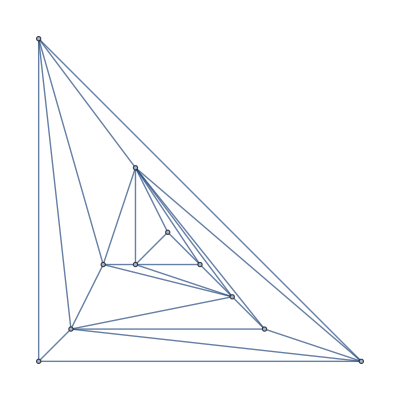

```mathematica
Graph[ReadGrof[604], GraphLayout->"PlanarEmbedding"]
```

```mathematica
cont[[1]]
```

```mathematica
Map[With[{cont=Read[StringToStream[#[[5]]],Expression]},
PaintGraph2First[ ReadGrof[#[[3]]],
Criterion[cont[[2]],cont[[3]]],
VertexLabels->"Name",
PlotLabel->"From " <> ToString[#[[1]]]<>" to " <> ToString[#[[2]]] <> " on edge " <> ToString[cont[[2]]],
GraphHighlight->{cont[[2]]},
GraphHighlightStyle->"Dashed",
ImageSize->250 ]]&,Select[biko,#[[6]]==False&&#[[7]]==10&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[With[{cont=Read[StringToStream[#[[5]]],Expression]},
cont[[2]]]&,Select[biko,#[[6]]==False&&#[[7]]==10&]]
```

{3<->6,3<->6,2<->6,2<->6,2<->6,2<->6,3<->6,2<->6,2<->6,3<->6,4<->6,1<->5}

```mathematica
FindInstance
```

```mathematica
Solve[ (1<=x1 <=4) && (1<=x2 <=4) && (1<=x3 <=4) && (1<=x5 <=4) && (1<=x7 <=4) && (1<=x8 <=4) && (1<=x6 <=4) && (1<=x4 <=4) && (1<=x9 <=4) && (1<=x10 <=4) && x1==1&x2==2&x3==3 && x1!=x2 && x1!=x3 && x1!=x5 && x1!=x7 && x1!=x8 && x2!=x3 && x2!=x6 && x2!=x7 && x3!=x4 && x3!=x6 && x3!=x8 && x3!=x9 && x3!=x10 && x4!=x5 && x4!=x9 && x4!=x10 && x5!=x6 && x5!=x7 && x5!=x8 && x5!=x9 && x5!=x10 && x6!=x7 && x6!=x9 && x8!=x10, {x1, x2, x3, x5, x7, x8, x6, x4, x9, x10},Integers]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x3 (1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x5≤4&&1≤x7≤4&&1≤x8≤4&&1≤x6≤4&&1≤x4≤4&&1≤x9≤4&&1≤x10≤4&&x1==1& x2==2&)==3&&x1≠x2&&x1≠x3&&x1≠x5&&x1≠x7&&x1≠x8&&x2≠x3&&x2≠x6&&x2≠x7&&x3≠x4&&x3≠x6&&x3≠x8&&x3≠x9&&x3≠x10&&x4≠x5&&x4≠x9&&x4≠x10&&x5≠x6&&x5≠x7&&x5≠x8&&x5≠x9&&x5≠x10&&x6≠x7&&x6≠x9&&x8≠x10,{x1,x2,x3,x5,x7,x8,x6,x4,x9,x10},Integers]

```mathematica
"{2,3<->6,2<->4}"
```

```mathematica
Map[With[{cont=Read[StringToStream[#[[5]]],Expression]},
PaintGraph2First[ ReadGrof[#[[3]]],
Criterion[cont[[2]],cont[[3]]],
VertexLabels->"Name",
PlotLabel->"From " <> ToString[#[[1]]/24]<>" to " <> ToString[#[[2]]/24] <> " on edge " <> ToString[cont[[2]]],
GraphHighlight->{cont[[2]]},
GraphHighlightStyle->"Dashed",
ImageSize->250 ]]&,Select[biko,#[[6]]==False&&#[[7]]==10&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}